```mathematica
ClearAll["Global`*"];
U1=10+5.6ⅉ;
I1=0.1+0.03ⅉ;
Z1=U1/I1
```

107.156+23.8532 ⅈ

```mathematica
ClearAll["Global`*"];
Z3RL=2000+300ⅉ;
ω3=100;

Z4RC=800-500ⅉ;
ω4=10000;

R3=Re[Z3RL]
L3=Im[Z3RL]/ω3

R4=Re[Z4RC];
Solve[Im[Z4RC]==-1/(C4*ω4),C4][[1]]
```

2000

3

{C4→1/5000000}

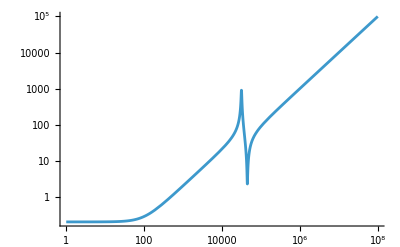

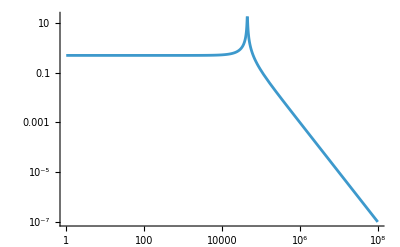

```mathematica
ClearAll["Global`*"];
r1=0.1;r3=0.1;r2=10^3;
l1=10^-3;l2=10^-3;c=10^-6;

zr1=r1;zr2=r2; zr3=r3;
zl1=ⅉ*ω*l1;zl2=ⅉ*ω*l2;
zc=1/(ⅉ*ω*c);

zr1l1=zr1+zl1;
zr3l2=zr3+zl2;
zr2r3l2c=1/(1/zr2+1/zr3l2+1/zc);

zin=zr1l1+zr2r3l2c;

a=zr2r3l2c/zin;

(*
a: prenos;
a = z2/(z1+z2);
*)

LogLogPlot[Abs[zin],{ω,1,10^8}]
LogLogPlot[Abs[a],{ω,1,10^8}]
```

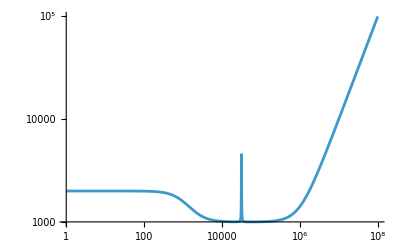

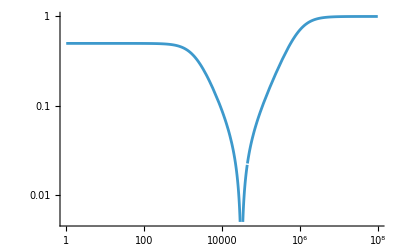

```mathematica
ClearAll["Global`*"];
r1=0.1;r2=0.1;r3=1000;r4=1000;
l1=10^-3;l2=10^-3;c1=10^-6;c2=10^-6;

zr1=r1;zr2=r2;zr3=r3;zr4=r4;
zl1=ⅉ*ω*l1; zl2=ⅉ*ω*l2;
zc1=1/(ⅉ*ω*c1);zc2=1/(ⅉ*ω*c2);

zr1c1=zr1+zc1;
zr2l1=zr2+zl1;
zr1c1r2l1=1/(1/zr1c1+1/zr2l1);
za=zr1c1r2l1+zr3;

zr4c2=1/(1/zr4+1/zc2);
zb=zl2+zr4c2;

zin=za+zb;
a=zb/zin;


LogLogPlot[Abs[zin],{ω,1,10^8}]
LogLogPlot[Abs[a],{ω,1,10^8}]
```